```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51f (14 June 2017)) loaded Wed 14 Jun 2017 16:42:30
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## SimRange-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

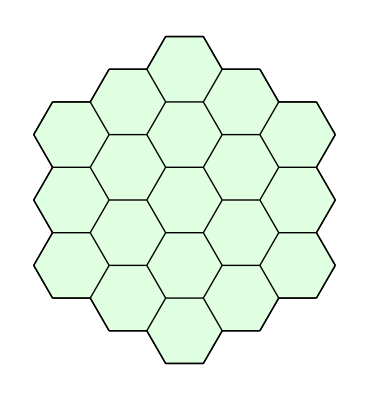

```mathematica
w=TemplateCircularHoneycombCover[3];
ShowTissue[w]
```

## Set up a model and run a simulation

```mathematica
n=NTissueCells[w]; 
net={{∅⇄A,k1, k2},{2 A+B->3 A,k3},{A->B,k4}, {A-> A+X, 1}};
parameters={k1-> .1, k2-> .1, k3-> .1 ,k4-> .3};
ic[i_]:={A[i]->RandomReal[{0,5}],B[i]->RandomReal[{0,5}], X[i]-> 0};
myic=Flatten[ic/@Range[n]];
bignet=CelleratorNetwork[w, "Reactions"-> net, "Diffiusion"-> {{A,DA}, {B, DB}}];
```

19 Cells.

5 internal reactions in each cell.

95 intracellular reactions.

0 diffusion reactions.

95 total reactions.

```mathematica
sim=RunSim[bignet/.{DB->.05, DA-> .1},parameters,myic,{0,50}];
```

## Use SimPlot to plot everything

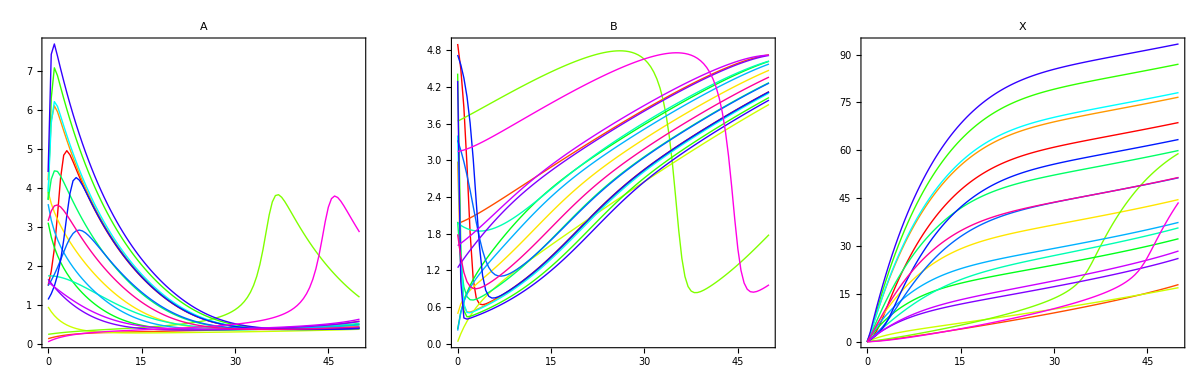

```mathematica
GraphicsRow[SimPlot[sim]]
```

## Use SimRange to get range of values

```mathematica
SimRange[sim, A, 10]
```

{0.288869,3.43685}

Get the range of A over the times {0, 1, 2, 3, 4, 5,  ... ,48,  49,  50}

```mathematica
SimRange[sim, A, {0, 50, 1}]
```

{0.0545516,7.6938}

Get the range of A over the times {0, 10, 20, 30, 40, 50}

```mathematica
SimRange[sim, A, {0, 50, 10}]
```

{0.0545516,4.40861}